```mathematica
r= {0.4,0.1};
b={{0.05,0.1},{0.08,0.003}};
dx1[x1_,x2_]:=r[[1]] * x1 -b[[1,1]]*(x1)^2-b[[1,2]]*x1*x2;
dx2[x1_,x2_]:=-r[[2]] * x2 -b[[2,2]]*(x2)^2+b[[2,1]]*x1*x2;
cond = {x1[0]==1.0,x2[0]==4.0};
res=NDSolve[{x1'[t]==r[[1]] * x1[t] -b[[1,1]]*(x1[t])^2-b[[1,2]]*x1[t]*x2[t], x2'[t]==-r[[2]] * x2[t] -b[[2,2]]*(x2[t])^2+b[[2,1]]*x1[t]*x2[t],cond},{x1,x2},{t,0,160}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
data = Import["ExplicitEuler.dat"]; (*ExplicitEuler,ImplicitEuler,Symmetrical,Runge_Kutta_4,Adams_Bashforth,*)
```

D:\BMSTU_coopmode_labs\Numerical_methods_6\Lab1\output

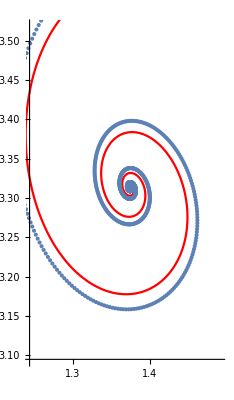

```mathematica
Show[ParametricPlot[Evaluate[{x1[t],x2[t]}/.res],{t,0,160},PlotStyle->Red],ListPlot[data]]
```

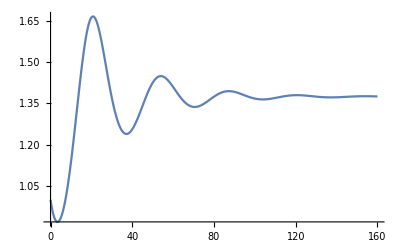

```mathematica
Plot[Evaluate[x1[t]/.res],{t,0,160},PlotRange->All]
```

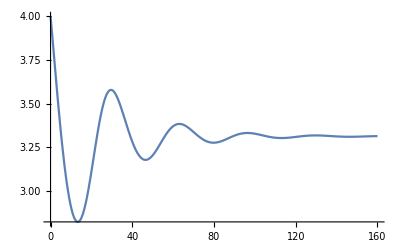

```mathematica
Plot[Evaluate[x2[t]/.res],{t,0,160},PlotRange->All]
```